```mathematica
KroneckerProduct[IdentityMatrix[3],spinx[1/2]].KroneckerProduct[spinx[1],IdentityMatrix[2]]//MatrixForm
```

(0 | 0 | 0 | 1/(2 √2) | 0 | 0
0 | 0 | 1/(2 √2) | 0 | 0 | 0
0 | 1/(2 √2) | 0 | 0 | 0 | 1/(2 √2)
1/(2 √2) | 0 | 0 | 0 | 1/(2 √2) | 0
0 | 0 | 0 | 1/(2 √2) | 0 | 0
0 | 0 | 1/(2 √2) | 0 | 0 | 0)

```mathematica
testmat=KroneckerProduct[IdentityMatrix[2],spinx[1/2]]+KroneckerProduct[spinx[1/2],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],spinz[1/2]].KroneckerProduct[spinz[1/2],IdentityMatrix[2]];
```

```mathematica
KroneckerProduct[IdentityMatrix[2],spinz[1/2]]+KroneckerProduct[spinz[1/2],IdentityMatrix[2]]+KroneckerProduct[IdentityMatrix[2],spinx[1/2]].KroneckerProduct[spinx[1/2],IdentityMatrix[2]]//MatrixForm
```

(-1 | 0 | 0 | 1/4
0 | 0 | 1/4 | 0
0 | 1/4 | 0 | 0
1/4 | 0 | 0 | 1)

```mathematica
MatrixExp[I*Pi/2(KroneckerProduct[IdentityMatrix[2],spiny[1/2]]+KroneckerProduct[spiny[1/2],IdentityMatrix[2]])].testmat.MatrixExp[-I*Pi/2(KroneckerProduct[IdentityMatrix[2],spiny[1/2]]+KroneckerProduct[spiny[1/2],IdentityMatrix[2]])]//MatrixForm
```

(-1 | 0 | 0 | 1/4
0 | 0 | 1/4 | 0
0 | 1/4 | 0 | 0
1/4 | 0 | 0 | 1)

```mathematica
rwaham3=testmat
rwaham3//MatrixForm
```

{{1/4,1/2,1/2,0},{1/2,-1/4,0,1/2},{1/2,0,-1/4,1/2},{0,1/2,1/2,1/4}}

(1/4 | 1/2 | 1/2 | 0
1/2 | -1/4 | 0 | 1/2
1/2 | 0 | -1/4 | 1/2
0 | 1/2 | 1/2 | 1/4)

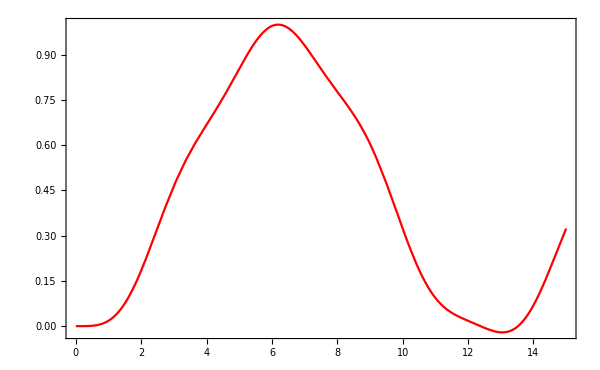

```mathematica
ρ=KroneckerProduct[spinx[1/2],IdentityMatrix[2]];
rhosol2=MatrixExp[-I*rwaham3*t].ρ.MatrixExp[I*rwaham3*t];
dat=(Tr[KroneckerProduct[IdentityMatrix[2],spinx[1/2]].#]&)@rhosol2;
Plot[dat,{t,0,15.001},PlotStyle->{Blue,Red},PlotRange->All]
```